```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/Jenna/jennaproject/mma

```mathematica
Needs["Integrals`"]
```

Needs::nocont: Context Integrals` was not created when Needs was evaluated.

```mathematica
mp0=Import["../data/test_matterPower_0.dat","Table"];
trlist=Import["../data/Tru_Tm.txt","Table"];
h=0.703;
```

```mathematica
size=Dimensions[mp0][[1]]
α=Log[mp0[[2,1]]/mp0[[1,1]]]/Log[mp0[[2,2]]/mp0[[1,2]]]
β=Log[mp0[[size,2]]/mp0[[size-1,2]]]/Log[mp0[[size,1]]/mp0[[size-1,1]]]
```

496

1.03608

-2.44708

```mathematica
Pm=Interpolation[mp0];
tr=Interpolation[trlist];
```

```mathematica
Dimensions[trlist]
```

{140,2}

```mathematica
Pmgood[k_]:=If[k<0.0001||k>1.993,0,Pm[k]];
Trgood[k_]:=If[k<1.9755223192*^-7||k>12.477498542,0,tr[k]];
```

```mathematica
Plot[(1+r^2)/(2r),{r,0,5}];
```

```mathematica
Limit[(r-μ)/(1+r^2-2r*μ)^(1/2),r->1]/.μ->1
```

0

```mathematica
Limit[(3r+7μ-10r*μ^2)/(14*r*(1+r^2-2r*μ)),r->1]/.μ->1
```

13/28

```mathematica
(*Clear[S]
S=#^3/(2*Pi^2)*(fgps[#,Pmgood]+fgps2[#,Pmgood])&/@Take[trlist,{1,110,10}][[All,1]];*)
```

```mathematica
autoru[0.01,Pmgood]
```

Suave::success: Needed 28000 function evaluations on 28 subregions.

1.54429×10^9

```mathematica
(*aru=#^3/(2*Pi^2)*autoru[#,Pmgood]&/@Take[trlist,{1,110,10}][[All,1]];*)anl=#^3/(2*Pi^2)*autonl[#,Pmgood]&/@Take[trlist,{1,110,10}][[All,1]];
(*crs=#^3/(2*Pi^2)*cross[#,Pmgood]&/@Take[trlist,{1,110,1}][[All,1]];*)
```

Suave::success: Needed 50135 function evaluations on 50 subregions.

Suave::success: Needed 50098 function evaluations on 50 subregions.

Suave::success: Needed 50064 function evaluations on 50 subregions.

General::stop: Further output of Suave will be suppressed during this calculation.

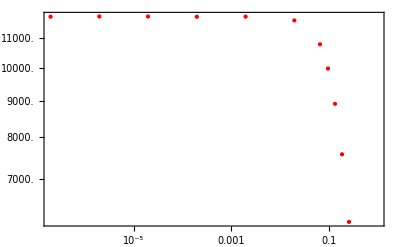

```mathematica
(*γ1=ListLogLogPlot[Thread[{Take[trlist[[All,1]],{1,110,10}],Abs[aru]/h^3}],Frame->True,PlotStyle->{Thick,Red}]*)
γ2=ListLogLogPlot[Thread[{Take[trlist[[All,1]],{1,110,10}],Abs[anl]/h^3}],Frame->True,PlotStyle->{Thick,Red}]
(*γ3=ListLogLogPlot[Thread[{Take[trlist[[All,1]],{1,110,1}],Abs[crs]/h^3}],Frame->True,PlotStyle->{Thick,Green}]
γall=ListLogLogPlot[Thread[{Take[trlist[[All,1]],{1,110,10}],S/h^3}],Frame->True,PlotStyle->{Thick,Blue}]*)
```

```mathematica
Show[γ1,γ2,γ3,γall]
```

Show::gcomb: Could not combine the graphics objects in ….

Show[γ1,-Graphics-,γ3,γall]